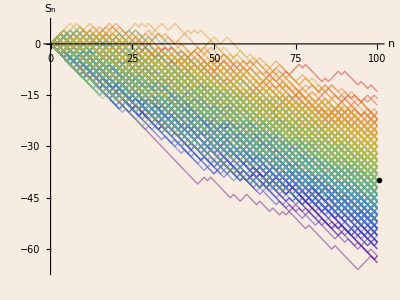

/Users/elvis/Documents/DSI/courses/content/stochastic-approximations/images/asymmetric_left_random_walks_1d_hist.svg

```mathematica
Options[svgExport]={"CommentString"->"Created by Mathematica",AspectRatio->Automatic,Background->Automatic};
Clear[svgExport];
svgExport[name_String,gr_,opts:OptionsPattern[]]:=Module[{svgCode=StringReplace[ExportString[First@ImportString[ExportString[gr,"PDF",Background->OptionValue[Background]],"PDF"],"SVG",Background->OptionValue[Background]],"<svg "->"<svg "<>If[OptionValue[AspectRatio]===Full," preserveAspectRatio='none' "," "]]&[ToString/@ImageDimensions[Rasterize[Show[gr,ImagePadding->0],"Image"]]]},Export[name,StringReplace[svgCode,RegularExpression["(<svg\\b[^>]*>)"]:>"$1"<>"\n<!-- ***Exported Comment***\n"<>OptionValue["CommentString"]<>"\n***Exported Comment*** -->"],"Text"]]

SeedRandom[1234];
data=RandomFunction[RandomWalkProcess[.3],{100},500];
sd=data["SliceData",100];
cf=ColorData["Rainbow"];sliced=BarChart[Last[#],Axes->False,BarOrigin->Left,AspectRatio->4,ChartStyle->(cf/@Rescale[MovingAverage[First[#],2],{Min[sd],Max[sd]},{0,1}]),ImageSize->60]&[HistogramList[sd,{Range[Min[sd],Max[sd],(Max[sd]-Min[sd])/15]}]];
plot = ListLinePlot[data,ImageSize->400,PlotRange->All,AspectRatio->3/4,
Background->RGBColor[247/255,236/255,226/255], AxesLabel->{HoldForm[n],HoldForm[Subscript[S,n]]},Epilog->Inset[sliced,{100.5,Mean[sd]},{0,8}],PlotStyle->(cf/@Rescale[sd]),
BaseStyle->Directive[Thin,Opacity[0.5]],AxesStyle->Opacity[1], PlotRangePadding->{{0,20},{.5,7}}]

svgExport["/Users/elvis/Documents/DSI/courses/content/stochastic-approximations/images/asymmetric_left_random_walks_1d_hist.svg",plot, AspectRatio->Full]
```

-Graphics3D-

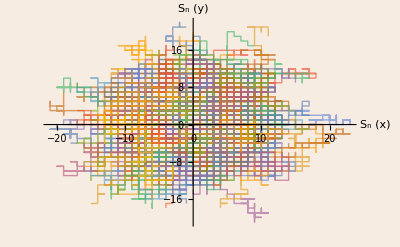

```mathematica
(*2d Random walk*)
Make3d[plot_,height_,opacity_]:=Module[{newplot},newplot=First@Graphics[plot];
newplot=N@newplot/.{x_?AtomQ,y_?AtomQ}:>{x,y,height};
newplot/.GraphicsComplex[xx__]:>{Opacity[opacity],GraphicsComplex[xx]}]

steps = 100;
numwalks = 500;
Randomwalk[n_]:=NestList[#+RandomChoice[{{1,0},{-1,0},{0,1},{0,-1}}]&,{0,0},n]
RandomwalkFixedSlice[n_] := Randomwalk[steps][[steps,All]]
RandomwalkFixed[n_] := Randomwalk[steps]
walks = Array[RandomwalkFixed, numwalks];
GetData[n_] := walks[[n,steps, All]];
slices = Array[GetData, numwalks];
hist = Histogram3D[slices, ChartStyle->Directive[White, Opacity[.4]],Axes->{False, False, False}];
lp = ListLinePlot[walks, BaseStyle->Directive[Thin,Opacity[0.65]],AxesLabel->{HoldForm[Subscript[S,n]"(x)"],HoldForm[Subscript[S,n]"(y)"]},Background->RGBColor[247/255,236/255,226/255]];
Show[{Graphics3D[Make3d[lp,0,.75], ImageSize->400],hist},Axes->True, Boxed->False,Background->RGBColor[247/255,236/255,226/255], AxesLabel->{HoldForm[Subscript[S,n]"(x)"],HoldForm[Subscript[S,n]"(y)"],""}]
lp
```

```mathematica
svgExport["/Users/elvis/Documents/DSI/courses/content/stochastic-approximations/images/symmetric_random_walks_2d_hist.svg",-Graphics3D-, AspectRatio->Full]
```

/Users/elvis/Documents/DSI/courses/content/stochastic-approximations/images/symmetric_random_walks_2d_hist.svg